```mathematica
p=3;
knots={0,0,0,0,.25,.3,1,1,1,1};
controlpoints={0,3,.5,1,0,1};
myspline[x_]:=Sum[controlpoints[[i+1]] BSplineBasis[{p,knots},i,x],{i,0,5}];
Grid@Table[Plot[myspline[x],{x,0,1},PlotPoints->NN,MaxRecursion->lambda,Method->{"Refinement"->{"ControlValue"->.1}},PlotRange->{{0,1},{0,1.6}}],{lambda,{0,1,2}},{NN,{5,10}}]
```

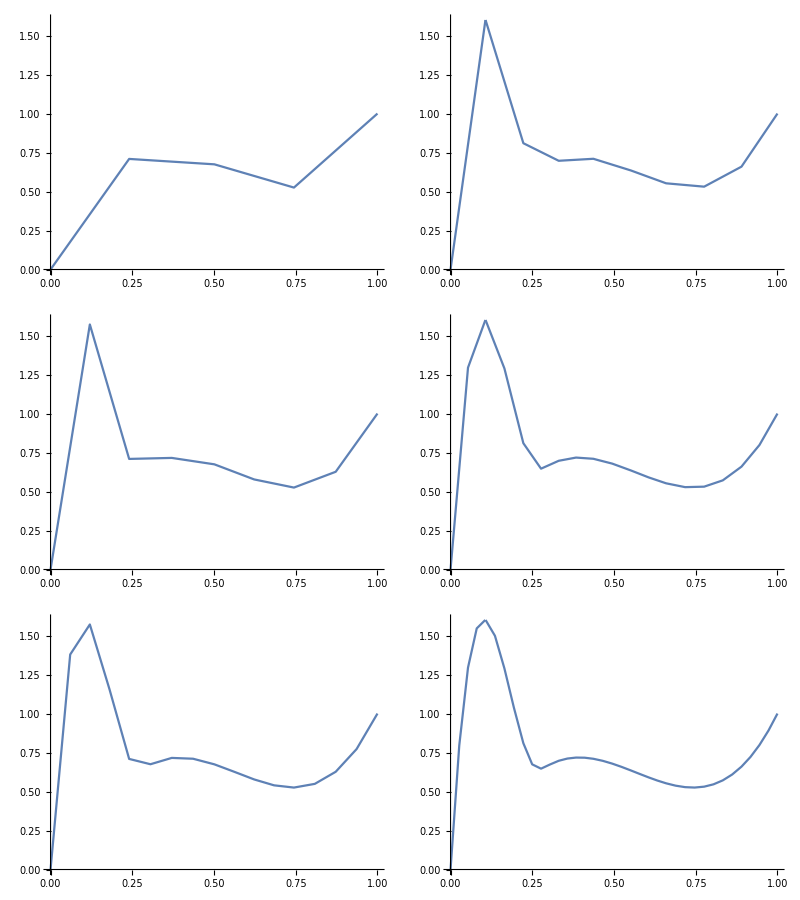
```mathematica
-Graphics-
Export["yyyyyy.eps",%]
```

-Graphics-

yyyyyy.eps

```mathematica
Plot[Abs[Sin[x]],{x,0,2 π},PlotPoints->5,MaxRecursion->1,Method->{"Refinement"->{"ControlValue"->0.1}}]

Plot[Abs[Sin[x]],{x,0,2 π},PlotPoints->10,MaxRecursion->2,Method->{"Refinement"->{"ControlValue"->0.1}}]

Plot[Abs[Sin[x]],{x,0,2 π},PlotPoints->6,MaxRecursion->3,Method->{"Refinement"->{"ControlValue"->.001}}]

knotaverages=Table[1/p*Sum[knots[[i]],{i,j+1,j+p}],{j,1,6}];
ListLinePlot[Table[{knotaverages[[i]],controlpoints[[i]]},{i,1,6}]]
```